```mathematica
;
```

Last updated:   Thu 9 Jun 2022

## General

```mathematica
Once@
```

WolframAlphaQueryResults

## URLS

```mathematica
(* home & meta pages *)
homeURL=URL["https://notes.martinssamuel.com/"];
metaURL=URL["https://notes.martinssamuel.com/meta"];
```

```mathematica
(* snapshots of home & meta pages *)
```

-Graphics--Graphics-

```mathematica
(* collage of homepage images (none at the moment) *)
(*ResourceFunction["WebPageImageCollage"]@homeURL⟦1⟧*)
```

```mathematica
(* check hyperlinks on homepage *)
hyperlinkDS=Once@;
hyperlinkDS=Once[/@hyperlinkDS];
```

https://martinssamuel.com/ | https://notes.martinssamuel.com/meta
https://notes.martinssamuel.com/ | https://notes.martinssamuel.com/poems-by-adrienne-rich
https://notes.martinssamuel.com/about | https://notes.martinssamuel.com/silence
https://notes.martinssamuel.com/dynamic | https://notes.martinssamuel.com/wolfram-notebooks
https://notes.martinssamuel.com/explanations | https://www.algolia.com/?utm_source=react-instantsearch&utm_medium=website&utm_content&utm_campaign=poweredby
https://notes.martinssamuel.com/historical-perspective |

## Graphs

### External links

```mathematica
(* func for highlighting longest path(s) in a graph *)
highlightLongestPaths@graph_:=;
```

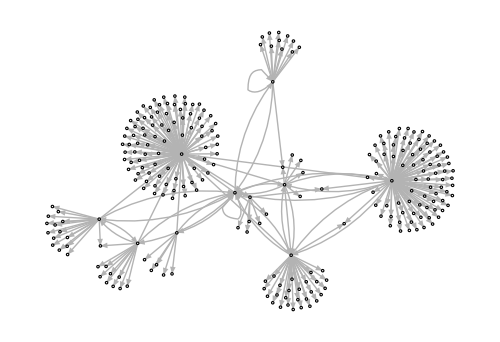

```mathematica
(* level-2 nested graph incl. external links; homePage===aboutPage ∴ ./ ⟦2⟧ w/ ⟦1⟧ *)
gExt=Once@
```

```mathematica
(* longest paths (incl. external links) *)
highlightLongestPaths@gExt
```

notes.martinssamuel.com/poems-by-adrienne-rich→ « 4 nodes » →notes.martinssamuel.com/dynamic
-Graphics-
Go to path URL »https://notes.martinssamuel.com/poems-by-adrienne-rich?stackedPages=%2Fsilence&stackedPages=%2Fabout&stackedPages=%2Fwolfram-notebooks&stackedPages=%2Fmeta&stackedPages=%2FdynamicNonehttps://notes.martinssamuel.com/poems-by-adrienne-rich?stackedPages=%2Fsilence&stackedPages=%2Fabout&stackedPages=%2Fwolfram-notebooks&stackedPages=%2Fmeta&stackedPages=%2FdynamicHyperlink1
There are 2927 other possible paths.

### Internal links

```mathematica
(* level-3 nested graph (internal links only) *)
gInt=Once@
(*method 2: *)
```

-Graphics-

```mathematica
(* longest paths (internal links only) *)
(* [this is a really inefficient way to this — computation gets exponentially larger as no. of nodes increase!!!] *)
(* try FindLongestPath — https://resources.wolframcloud.com/FunctionRepository/resources/FindLongestPath *)
highlightLongestPaths[gInt]
```

notes.martinssamuel.com/listening→ « 13 nodes » →notes.martinssamuel.com/historical-perspective/books
-Graphics-
Go to path URL »https://notes.martinssamuel.com/listening?stackedPages=%2Fsilence&stackedPages=%2Fadrienne-rich&stackedPages=%2Fpoems-by-adrienne-rich&stackedPages=%2Fbooks&stackedPages=%2Fsmall-is-beautiful&stackedPages=%2Fabout&stackedPages=%2Fdynamic&stackedPages=%2Fmeta&stackedPages=%2Fnote-taking&stackedPages=%2Fwolfram-notebooks&stackedPages=%2Fart&stackedPages=%2Fexploration&stackedPages=%2Fhistorical-perspective&stackedPages=%2FbooksNonehttps://notes.martinssamuel.com/listening?stackedPages=%2Fsilence&stackedPages=%2Fadrienne-rich&stackedPages=%2Fpoems-by-adrienne-rich&stackedPages=%2Fbooks&stackedPages=%2Fsmall-is-beautiful&stackedPages=%2Fabout&stackedPages=%2Fdynamic&stackedPages=%2Fmeta&stackedPages=%2Fnote-taking&stackedPages=%2Fwolfram-notebooks&stackedPages=%2Fart&stackedPages=%2Fexploration&stackedPages=%2Fhistorical-perspective&stackedPages=%2FbooksHyperlink1
There are 215 other possible paths.

```mathematica
(* connected components *)
```

-Graphics-

```mathematica
(* communities *)
CommunityGraphPlot[gInt,FindGraphCommunities[gInt]]
```

-Graphics-

```mathematica
plotOpts=;
HighlightGraphProperty[g_,prop_,opts___]:=;
```

```mathematica
(* vertex degree *)
HighlightGraphProperty[gInt,VertexDegree]
```

VertexDegree
https://notes.martinssamuel.com | 30.
https://notes.martinssamuel.com/wolfram-notebooks | 21.
https://notes.martinssamuel.com/poems-by-adrienne-rich | 12.
https://notes.martinssamuel.com/silence | 12.
https://notes.martinssamuel.com/exploration | 11.
-Graphics-

```mathematica
(* betweenness centrality *)
HighlightGraphProperty[gInt,BetweennessCentrality]
```

BetweennessCentrality
https://notes.martinssamuel.com | 464.
https://notes.martinssamuel.com/wolfram-notebooks | 285.2
https://notes.martinssamuel.com/poems-by-adrienne-rich | 117.2
https://notes.martinssamuel.com/silence | 103.7
https://notes.martinssamuel.com/exploration | 95.3
-Graphics-

```mathematica
(* k-core components *)
```

```mathematica
(* independent vertex & edge sets *)
```

{-Graphics-,-Graphics-}

```mathematica
(* vertex & edge covers *)
```

{-Graphics-,-Graphics-}

```mathematica
(* cliques *)
```

-Graphics-

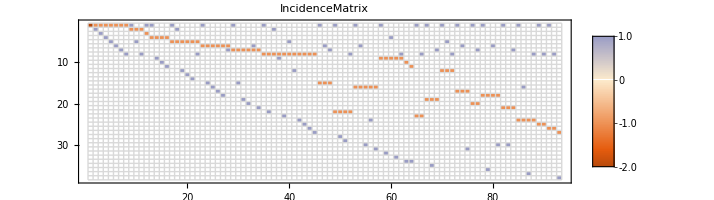
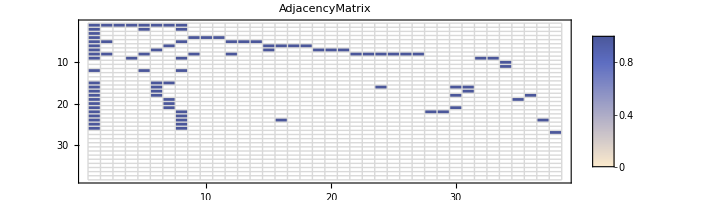
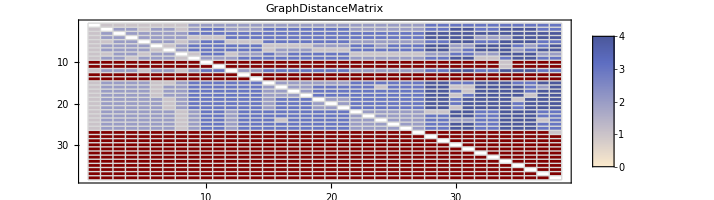

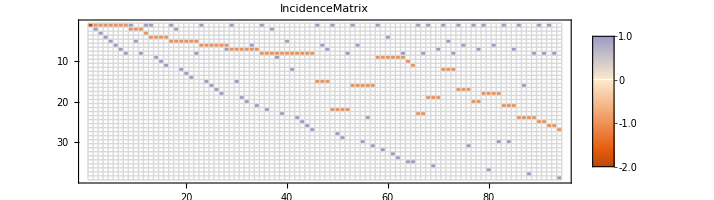
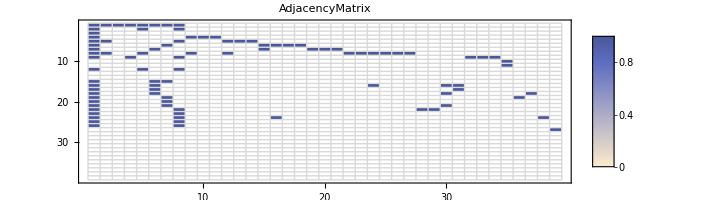
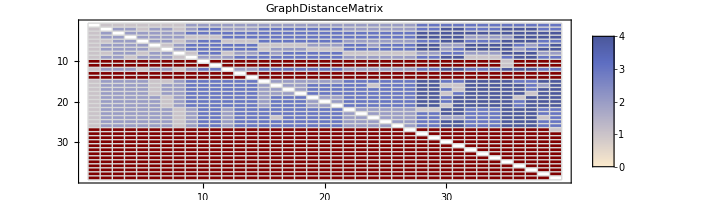

-Graphics-
-Graphics-
-Graphics-

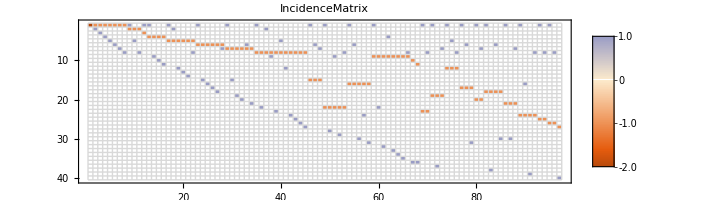
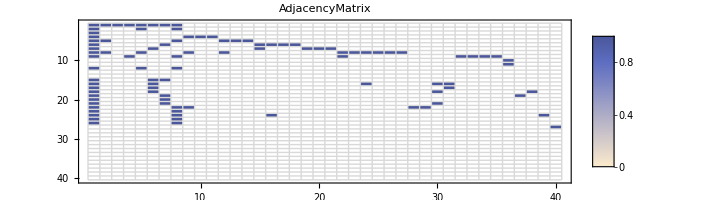
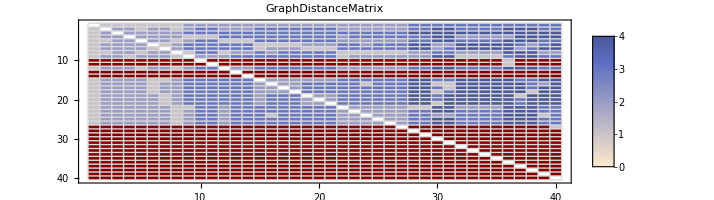

```mathematica
(* grpah matrices *)
```